## Mathematical Modeling of a Whammy Bar Kalimba

#### Allan Struthers, Michigan Tech

The kalimba, an African lamellaphone, produces sound via vibrating metal tines. This study develops a linear PDE model for kalimba tines with a novel “”whammy-bar”” support from standard beam theory with non-standard boundary conditions, the PDE is discretized using a five-point stencil, yielding an ODE system: u’’ = Au + f. The eigenvalues and eigenvectors of A predict frequencies, spectral tonality, and mode shapes. Model predictions for a fixed support will be compared to a standard kalimba, and 
the tonal characteristics of the whammy-bar kalimba will be demonstrated.

## What is a kalimba?

-Graphics-

Small beams, firmly cantilevered over a metal bridge linked to a resonance chamber.  pic wiki.

Tuned by adjusting the cantilevered length

Model: Uniform Euler-Bernouili beam with

Built-In boundary conditions at the clamped end

Free-Free boundary conditions at the far end

The bridge is modelled as a point constraint

## What is a Whammy Bar?

A whammy bar alters the string-tension in an electric guitar to produce familiar effects.

## Guitar String Model

The undamped linearized Partial Differential Equation (PDE) for the transverse displacement u(x,t) of a guitar string under a constant tension T is the wave equation
(W)	ρ u_tt=T u_xx
with Boundary Conditions u(0,t)=u(L,t)=0 indicating zero displacement displacement at the bridge and the top of the neck x=L.

Middle C is roughly 261Hz.

Guitar tones decay and players alter string tension (using a whammy bar) on time scales significantly greater than 1/261 of a second.

A quasi-static approximation to a lightly-damped string under slowly varying tension uses the resonant frequencies and mode shapes of the constant undamped system as building blocks.

## Guitar Discretization

The wave equation is discretized by subdividing 0≤x≤L into n equal subdivisions
	x_i=0+i Δx  with Δx=1/(n+1)
and approximating the second derivative at x_i with the symmetric centered second difference  
	u_xx(x_i,t)≈(u(x_i-Δx,t)-2u(x_i,t)+u(x_i+Δx,t))/Δx^2
Substituting this Finite Difference (FD) approximation into the wave equation gives 
(G) 	ρ(d^2 u_i)/dt^2=(u_(i-1)-2 u_i+u_(i+1))/Δx^2  or equivalently u''=-T/(ρ Δx^2)A.u where 
	A=(2 | -1 |   |  
-1 | 2 | -1 |  
  | ⋱ | ⋱ | -1
  |   | -1 | 2)

Note: The boundary conditions u_0=u_(n+1)=1 are built into the n×n symmetric tridiagonal n×n A.  The single parameter T/ρ  characterizes the string: harp, double bass, piano, violin, harpsichord, etc.

## Eigen Stuff

If the pair (λ_i,v_i) satisfies A v_i=λ_i v_i then (c_i cos(ω_i t)+s_i sin(ω_i t))v_i with ω_i=√((T λ_i)/(ρ Δx^2))solves u''=-A.u

Eigenvalues of A give the approximate resonant frequencies ω_i=√((T λ_i)/(ρ Δx^2)) of the undamped instrument.

Eigenvectors of A give the approximate string profiles v_i for those frequencies.

Initial displacements u(0) and velocities u'(0) determine the coefficients c_i and s_i.  This alters tone as do details of the pickup and/or resonator.

## Eigen Pictures

Computed eigenvalues are always sorted from big to small!   Small eigenvalues and their eigenvectors determine the fundamental frequency and mode of the string.  with T=L=1.0 we have

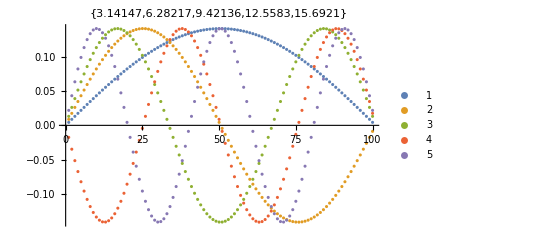

```mathematica
n=100;A=SparseArray[{Band[{1,1}]->2.0,Band[{1,2}]->-1.0,Band[{2,1}]->-1.0},{n,n}];
{λs,vs}=Sort[Eigensystem[A]ᵀ]ᵀ;ListPlot[ vs⟦1;;5⟧,PlotLegends->Automatic,Mesh->All,PlotLabel->√(λs⟦1;;5⟧ (n+1)^2)]
```

Approximate fundamental frequencies of π, 2 π, 3 π, …

The lowest frequency is the fundamental, then the second harmonic etc.

Approximate fundamental mode shapes of sin(π x_j), sin(2π x_j), sin(3 π x_j)

Plucking, bowing, or striking the string in different locations excites different harmonics.

All stringed instruments have this “harmonic” frequency spectrum.

## Kalimba Beam Model

The undamped linearized PDE for the transverse displacement u(x,t) of a beam is the Euler Bernoulli 
(EB)	ρ u_tt=Γ u_xxxx
Built-In BC are appropriate at the clamp x=0 
	u(0,t)=u_x(0,t)=0
Free-Free BC (indicating zero transverse load and moment) are appropriate at x=L
	u_xx(L,t)=u_xxx(L,t)=0.
To keep the beam firmly on the bridge (unlike the image above) at x=b we enforce 
	u(b,t)=0
The discretization is more complicated because of the boundary conditions and the requirement that x=b is a discretization point

## Free-Free Boundary Condition at x=0

The beam equation is discretized by subdividing both 0≤x≤b and b≤x≤L into equal subdivisions 
	x_i=0+i Δx_1  with Δx_1=b/(n_1+1) 		           for 1≤i≤n_1
	x_i=b+(i-n_1) Δx_2  with Δx_2= (L - b)/n_2 	for n_1+1≤i≤n_1+n_2
The symmetric centered fourth Finite Difference (FD) at a point x_i is 
	u_xxxx(x_i,t)≈(u(x_i-2h,t)-4u(x_i-h,t) + 6 u(x_i,t) -4u(x_i+h,t)+ u(x_i+2h,t))/h^4

At x=0 for u(0,t)=0 and u_x(0,t)=0 we introduce equations for ghost point
	u_0=0  and u_-1=u_1
 (that are eliminated) to  get
	u_xxxx(x_1)≈(u_(1-2)-4 u_(1-1)+ 6 u_1 -4 u_(1+1)+ u_(1+2))/(Δx_1)^4=(u_-1- 4 u_0+ 6 u_1 - 4 u_2+ u_3)/(Δx_1)^4=(7 u_1 - 4 u_2+ u_3)/(Δx_1)^4
	u_xxxx(x_2)≈(u_(2-2)-4 u_(2-1)+ 6 u_2 -4 u_(2+1)+ u_(2+2))/(Δx_1)^4=(u_0- 4 u_1+ 6 u_2 - 4 u_3+ u_4)/(Δx_1)^4=(- 4 u_1+ 6 u_2 - 4 u_3+ u_4)/(Δx_1)^4

## Free-Free Boundary Condition at x=L

For u_xx(L,t)=0 and u_xxx(L,t)=0 at x_(2n)=L introduce ghost points u_(n_1+n_2 + 1) and u_(n_1+n_2 + 2).  The B are
	(Δx_2)^2 u_xx(x_(n_1+n_2))≈u_(n_1+n_2 - 1)-2 u_(n_1+ n_2)+u_(n_1+ n_2 + 1)=0
	(Δx_3)^2 u_xxx(x_(n_1+ n_2))≈-1/2 u_(n_1+ n_2 - 2)+2 u_(n_1+ n_2-1)-u_(n_1+ n_2 + 1)+1/2 u_(n_1+ n_2+2)=0
which gives the ghosts (with m=n_1+n_2)
	u_(m + 1)=-u_(m - 1)+2 u_m
	u_(m + 2)=u_(m - 2)-6 u_(m - 1)+4 u_m
Substituting the ghosts into the standard centered difference gives the last two approximations
	u_xxxx(x_m)≈(u_(m - 2)-4 u_(m - 1)+ 6 u_m -4 u_(m+1)+ u_(m + 2))/(Δx_2)^4=(2 u_(m- 2)- 6 u_(m- 1)+ 2 u_m)/(Δx_2)^4
	u_xxxx(x_(m-1))≈(u_(m - 3)-4 u_(m - 2)+ 6 u_(m-1) -4 u_m+ u_(m + 1))/(Δx_2)^4=(u_(m- 3)- 4 u_(m- 2)+ 5 u_(m-1)-2 u_m)/(Δx_2)^4

```mathematica
Clear[n]
sol1=Solve[Subscript[u, m - 1]-2 Subscript[u, m]+Subscript[u, m+ 1]==0, Subscript[u, m + 1]]⟦1⟧
sol2=Simplify[Solve[-1/2 Subscript[u, m - 2]+2 Subscript[u, m-1]-Subscript[u, m + 1]+1/2 Subscript[u, m+2]==0,Subscript[u, m+2]]⟦1⟧/.sol1]
Simplify[(Subscript[u, m - 2]-4 Subscript[u, m - 1]+ 6 Subscript[u, m] -4 Subscript[u, m+1]+ Subscript[u, m + 2])/.sol1/.sol2 ]
Simplify[(Subscript[u, m - 3]-4 Subscript[u, m - 2]+ 6 Subscript[u, m-1] -4 Subscript[u, m]+ Subscript[u, m + 1])/.sol1/.sol2 ]
```

{u_(1+m)→-u_(-1+m)+2 u_m}

{u_(2+m)→u_(-2+m)-6 u_(-1+m)+4 u_m}

2 (u_(-2+m)-3 u_(-1+m)+u_m)

u_(-3+m)-4 u_(-2+m)+5 u_(-1+m)-2 u_m

```mathematica
[ u''''[x],Table[u[x+i h],{i,-2,2}],u,x]["Stencil"]
```

```mathematica
[ u''''[x],Table[u[x+i h],{i,-2,2}],u,x]
```

## Beam Discretization around x=b

At the bridge x=b we need u(b)=0. Using the ghost value u(b)=0 in the standard discretization gives
	u_xxxx(x_(n_1-2))=u_xxxx(b-2 Δx_1)≈(u_(n_1 -4)-4 u_(n_1-3)+ 6 u_(n_1-2) -4 u_(n_1-1)+ u(b))/(Δx_1)^4=(u_(n_1 -4)-4 u_(n_1 -3)+ 6 u_(n_1-2) -4 u_(n_1-1))/(Δx_1)^4 
and 
	u_xxxx(x_(n_1+1))=u_xxxx(b+2 Δx_2)≈(u(b)-4 u_n_1+ 6 u_(n_1+1) -4 u_(n_1+2)+u_(n_1+3))/(Δx_2)^4=(-4 u_n_1+ 6 u_(n_1+1) -4 u_(n_1+2)+u_(n_1+3))/(Δx_1)^4

The last things we need are approximations to 
	u_xxxx(x_(n-1))=u_xxxx(b-Δx_1) and u_xxxx(x_n)=u_xxxx(b+Δx_2)
These “uneven” FD approximations look cleaner if we write Δx_2=γ Δx_1
	u_xxxx(x_(n-1))=u_xxxx(b-Δx_1)≈(4 ((u_(n-3))/(3+γ)-(3 u_(n-2))/(2+γ)+(3 u_(n-1))/(1+γ)+(6 u_n)/(γ (6+11 γ+6 γ^2+γ^3))))/Δx1^4
	u_xxxx(x_(n+1))=u_xxx(b+Δx_2)≈(4 (6 γ^3 u_(n-1)+3 (1+5 γ+6 γ^2) u_n - (1+γ) ((3+9 γ) u_(n+1)-(1+2 γ) u_(n+2))))/(γ^3 (1+γ) (1+2 γ) (1+3 γ) Δx1^4) 
Although slightly complicated all you need to do is solve linear equations to match Taylor series coefficients.

```mathematica
Clear[Δx1]
[ u''''[x-Δx1],
{u[x-3 Δx1],u[x-2 Δx1],u[x-Δx1],u[x],u[x+γ Δx1]},u,x]["Stencil"]
```

-(4 u[x])/(γ Δx1^4)+(4 u[x-3 Δx1])/((3+γ) Δx1^4)-(12 u[x-2 Δx1])/((2+γ) Δx1^4)+(12 u[x-Δx1])/((1+γ) Δx1^4)+(24 u[x+γ Δx1])/(γ (6+11 γ+6 γ^2+γ^3) Δx1^4)

## Kalimba Matrix

```mathematica
(u(Subscript[x, i]-2h,t)-4u(Subscript[x, i]-h,t) + 6 u(Subscript[x, i],t) -4u(Subscript[x, i]+h,t)+ u(Subscript[x, i]+2h,t))/h^4
```

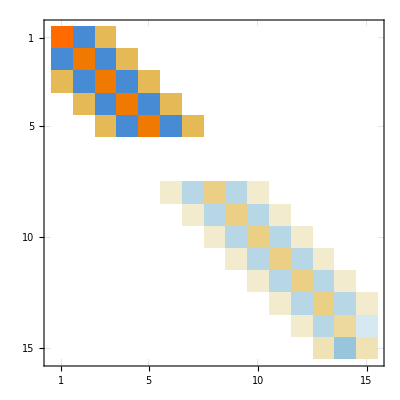

```mathematica
{b,L}={1.1,5.0};
{n1,n2}={7,8};m=n1+n2;
{Δx1,Δx2}={b/(n1+1),(L-b)/n2};
A=ConstantArray[0.0,{m,m}];
A⟦1,{1,2,3}⟧={7,-4,1}/Δx1^4;
A⟦2,{1,2,3,4}⟧={-4,6,-4,1}/Δx1^4;
Do[
A⟦i,{i-2,i-1,i,i+1,i+2}⟧={1,-4,6,-4,1}/Δx1^4,
{i,3,n1-2}]
Do[
A⟦i,{i-2,i-1,i,i+1,i+2}⟧={1,-4,6,-4,1}/Δx2^4,
{i,n1+1,m-2}]
A⟦m-1,{m-3,m-2,m-1,m}⟧={1,-4,5,-2}/Δx2^4;
A⟦m,{m-2,m-1,m}⟧={2,-6,2}/Δx2^4;
MatrixPlot[A,GridLines->Automatic]
```

```mathematica
{Δx1,Δx2}={b/(n1+1),(L-b)/n2};
x1vals=Table[i Δx1,{i,-1,n1}];
x2vals=Table[b+i Δx2,{i,1,2n+2}];
```

```mathematica
n=n1+n2
Length[x1vals]
Length[x2vals]
```

45

20

25

```mathematica
m=n1+n2;
A=ConstantArray[0.0,{m,m}];
A⟦1,{1,2,3}⟧={7,-4,1}/Δx1^4;
A⟦2,{1,2,3,4}⟧={-4,6,-4,1}/Δx1^4;
A⟦-1,{m-2,m-1,m}⟧={2,-6,2}/Δx2^4;
A⟦-2,{m-3,m-2,m-1,m}⟧={1,-4,5,-2}/Δx2^4;
```

```mathematica
Subscript[u, xxxx](Subscript[x, m])≈(Subscript[u, m - 2]-4 Subscript[u, m - 1]+ 6 Subscript[u, m] -4 Subscript[u, m+1]+ Subscript[u, m + 2])/(Subscript[Δx, 2])^4=(2 Subscript[u, m- 2]- 6 Subscript[u, m- 1]+ 2 Subscript[u, m])/(Subscript[Δx, 2])^4
	Subscript[u, xxxx](Subscript[x, m-1])≈(Subscript[u, m - 3]-4 Subscript[u, m - 2]+ 6 Subscript[u, m-1] -4 Subscript[u, m]+ Subscript[u, m + 1])/(Subscript[Δx, 2])^4=(Subscript[u, m- 3]- 4 Subscript[u, m- 2]+ 5 Subscript[u, m-1]-2 Subscript[u, m])/(Subscript[Δx, 2])^4
```

```mathematica
Subscript[u, xxxx](Subscript[x, 1])≈(Subscript[u, 1-2]-4 Subscript[u, 1-1]+ 6 Subscript[u, 1] -4 Subscript[u, 1+1]+ Subscript[u, 1+2])/(Subscript[Δx, 1])^4=(Subscript[u, -1]- 4 Subscript[u, 0]+ 6 Subscript[u, 1] - 4 Subscript[u, 2]+ Subscript[u, 3])/(Subscript[Δx, 1])^4=(7 Subscript[u, 1] - 4 Subscript[u, 2]+ Subscript[u, 3])/(Subscript[Δx, 1])^4
```

```mathematica
Table[
SparseArray[,{}]]
```

```mathematica
A=Join[
SparseArray[{2n}]
]
```

The matrix build can be automated fair easily,.  Make the including the 2+2+1 ghost points.

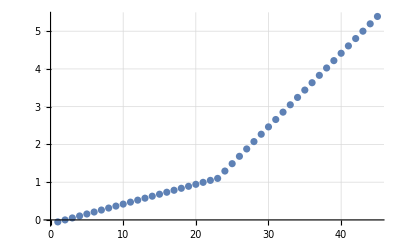

```mathematica
{b,L,n}={1.1,5.0,20};
{Δx1,Δx2}={b/(n+1),(L-b)/n};
xvals=Join[Table[i Δx1,{i,-1,n}],Table[b+(i-n) Δx2,{i,n, 2n+2}]];
Table[ 
[ u''''[x],Table[u[x+i h],{i,-2,2}],u,x]
ListPlot[Join[Table[i Δx1,{i,-1,n}],Table[b+(i-n) Δx2,{i,n, 2n+2}]],
GridLines->Automatic]
```

Since there are multiple possibilities to

Our ODE system is u''=A u where A is

```mathematica
A⟦1⟧=[ u''''[x],Table[u[x+i h],{i,-2,2}],u,x]
```

<|Stencil→(6 u[x])/h^4+u[-2 h+x]/h^4-(4 u[-h+x])/h^4-(4 u[h+x])/h^4+u[2 h+x]/h^4,Coefficients→{1/h^4,-4/h^4,6/h^4,-4/h^4,1/h^4},Order→1/6 h^2 u^(6)[x]|>

## Image Code

```mathematica
ConvertImageToFullyScaledNinePatch[img_]:=Module[{paddedImage=ImagePad[img,1,Black]},ReplaceImageValue[paddedImage,Flatten[Outer[List,{0,#1},{0,#2}]&@@ImageDimensions[paddedImage],1]->White]]
NotebookPut[Notebook[{},System`BackgroundAppearance->ConvertImageToFullyScaledNinePatch[-Graphics-]]]
```